Preamble

## Package Imports

```mathematica
AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace2\\NumberTheory"];
<<NumberTheory`
```

```mathematica
ComplexAnalysis`BranchPoints[√(z^2-1),z]
ComplexAnalysis`BranchCuts[√(z^2-1),z]
```

{-1,1,ComplexInfinity}

(-1<Re[z]<0&&Im[z]==0)||Re[z]==0||(0<Re[z]<1&&Im[z]==0)

## Examples

### Definition / Theorem

This is text.

#### Example

# Notes Elliptic Functions

0. Preliminaries

## 0.5 Infinite Products

1. Circular Functions

## 1.1 Eisenstein Series

### Definition

```mathematica
eisensteinSeries[k_,x_]:=Sum[1/(x+m)^k,{m,-Infinity,Infinity}]  (* 1.1 *)
eisensteinSeries[1,x_]:=1/x+Sum[(2x)/(x^2-m^2),{m,1,Infinity}] (* 1.2 *)
eisensteinSeries[x_]:=f[1,x] (* 1.2 *)
```

```mathematica
eisensteinSeries[x]
eisensteinSeries[2,x]
eisensteinSeries[3,x]
eisensteinSeries[4,x]
```

f[1,x]

π^2 Csc[π x]^2

π^3 Cot[π x] Csc[π x]^2

1/3 π^4 (2 Cot[π x]^2 Csc[π x]^2+Csc[π x]^4)

### Graphs

```mathematica
eisensteinSeries[2,0.6+0.3I]
eisensteinSeries[2,0.6+0.4I]
eisensteinSeries[2,0.9+0.01I]
```

4.21297+2.13838 ⅈ

2.41244+1.44284 ⅈ

100.404+19.5925 ⅈ

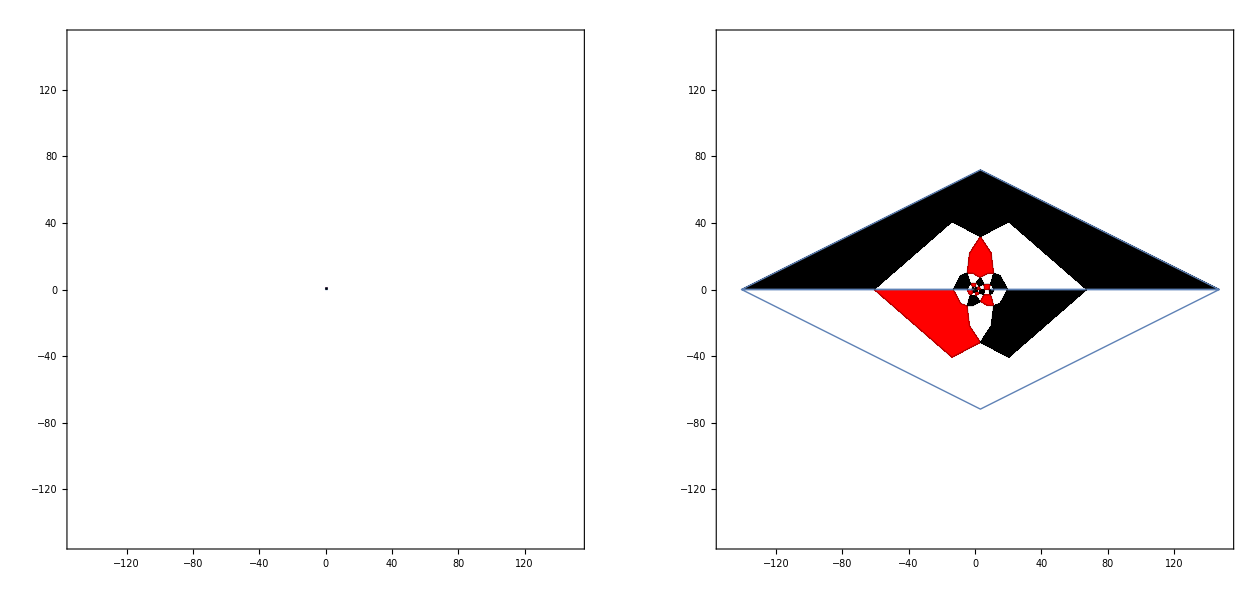

```mathematica
GraphicsRow[
With[{s=σ+I t},
ParametricPlot[ReIm@#[s],{σ,0,1},{t,0,1},
Axes->{True,True},
Frame->True,
Mesh->{7,7},
MeshShading->ArrayPad[{{None,Black},{Red,None}},{{0,0},{0,0}},None],
PlotRange->{{-150,150},{-150,150}},PlotPoints->{4,4}]
]&/@{Identity,eisensteinSeries[2,#]&}]
```

### Some Properties

E_k(x+n)=E_k(x)

```mathematica
eisensteinSeries[2,2.25]
eisensteinSeries[2,5.25]
```

19.7392

19.7392

E_1(1/2)=E_1(1/2+n)=0

```mathematica
eisensteinSeries[1,0.5]
eisensteinSeries[1,4.5]
```

0.

0.

(* 1.3 *)
If y < |d|=min(x,ℤ) Then
E_1(x+y)=∑_(k=0)^∞ (-y)^k E_(k+1)(x)=0

```mathematica
eisensteinSeries[1,2.25+0.05]
Sum[(-0.05)^k eisensteinSeries[k+1,2.25],{k,0,100}]//Chop  (* 1.3 *)
```

2.2825

2.2825

### Derivatives

(* 1.4 *)
E_(k+1)(x)=(-1)^k/(k!)E_1^(k)(x)

```mathematica
eisensteinSeries[5,2.25]
(D[eisensteinSeries[1,x],{x,4}]/.x:>2.25)(-1)^4/(4!)
```

1020.07

1020.07

E'_k(x)=-k E_(k+1)(x)

```mathematica
D[eisensteinSeries[3,x],{x,1}]//Simplify
-3 eisensteinSeries[4,x]//Simplify
```

-π^4 (2+Cos[2 π x]) Csc[π x]^4

-π^4 (2+Cos[2 π x]) Csc[π x]^4

(* 1.5 *)
If y < |d|=min(x,ℤ) Then
E_k(x+y)=∑_(m=k)^∞ (m-1
k-1)(-y)^(m-k)E_m(x)=0

```mathematica
eisensteinSeries[3,2.25+0.05]
Sum[(-0.05)^(m-3)Binomial[m-1,2]eisensteinSeries[m,2.25],{m,3,100}]//Chop
```

34.4188

34.4188

### Series Representation

(* 1.6 *)
E_1(x)=1/x-∑_(j=1)^∞ γ_(2 j)x^(2 j-1) where γ_(2 j)= 2∑_(n=1)^∞ 1/n^(2 j)

```mathematica
g[k_]:=2 Sum[1/n^k,{n,1,Infinity}]
```

```mathematica
Series[eisensteinSeries[1,x],{x,0,10}]
```

1/x-(π^2 x)/3-(π^4 x^3)/45-(2 π^6 x^5)/945-(π^8 x^7)/4725-(2 π^10 x^9)/93555+O[x]^11

```mathematica
Table[g[x],{x,2,10,2}]
```

{π^2/3,π^4/45,(2 π^6)/945,π^8/4725,(2 π^10)/93555}

(* 1.7 *)
E_k(x)=1/x^k+(-1)^k∑_(2j>=k)^∞ (2j-1
k-1)γ_(2 j)x^(2 j-k) where γ_(2 j)= 2∑_(n=1)^∞ 1/n^(2 j)

```mathematica
g1[k_]:=2Binomial[k-1,4] Sum[1/n^k,{n,1,Infinity}]
g2[k_]:=2Binomial[k-1,5] Sum[1/n^k,{n,1,Infinity}]
```

```mathematica
Series[eisensteinSeries[5,x],{x,0,10}]
```

1/x^5-(2 π^6 x)/189-(π^8 x^3)/135-(4 π^10 x^5)/1485-(2764 π^12 x^7)/3869775-(4 π^14 x^9)/25515+O[x]^11

```mathematica
Table[g1[x],{x,2,14,2}]
```

{0,0,(2 π^6)/189,π^8/135,(4 π^10)/1485,(2764 π^12)/3869775,(4 π^14)/25515}

```mathematica
Series[eisensteinSeries[6,x],{x,0,10}]
```

1/x^6+(2 π^6)/945+(π^8 x^2)/225+(4 π^10 x^4)/1485+(2764 π^12 x^6)/2764125+(4 π^14 x^8)/14175+(3617 π^16 x^10)/54219375+O[x]^11

```mathematica
Table[g2[x],{x,2,16,2}]
```

{0,0,(2 π^6)/945,π^8/225,(4 π^10)/1485,(2764 π^12)/2764125,(4 π^14)/14175,(3617 π^16)/54219375}

### Duplication Formula

(* 1.8 *)
n^k E_k(n x)=∑_(j=0)^(n-1) E_k(x+j/n)

```mathematica
5^3 eisensteinSeries[3,5 2.25]
Sum[eisensteinSeries[3,2.25+j/5],{j,0,4}]
```

#### Experiment

7751.57

7751.57

```mathematica
5^3 eisensteinSeries[3,5x]
Sum[eisensteinSeries[3,x+j/5],{j,0,4}]//TrigReduce//Simplify
Sum[eisensteinSeries[3,x+j/5],{j,0,4}]//FullSimplify
```

125 π^3 Cot[5 π x] Csc[5 π x]^2

(125 π^3 Cos[5 π x] Csc[π x]^3)/(1+2 Cos[2 π x]+2 Cos[4 π x])^3

π^3 (Cot[π x] Csc[π x]^2+Cot[π (1/5+x)] Csc[π (1/5+x)]^2-Cot[1/5 (π-5 π x)] Csc[1/5 (π-5 π x)]^2+Sec[π (1/10-x)]^2 Tan[π (1/10-x)]-Sec[π (1/10+x)]^2 Tan[π (1/10+x)])

```mathematica
125 π^3 Cot[5 π x] Csc[5 π x]^2/.x:>7.19
```

-999959.

```mathematica
(125 π^3 Cos[5 π x] Csc[π x]^3)/(1+2 Cos[2 π x]+2 Cos[4 π x])^3/.x:>7.19
```

-999959.

```mathematica
π^3 (Cot[π x] Csc[π x]^2+Cot[π (1/5+x)] Csc[π (1/5+x)]^2-Cot[1/5 (π-5 π x)] Csc[1/5 (π-5 π x)]^2+Sec[π (1/10-x)]^2 Tan[π (1/10-x)]-Sec[π (1/10+x)]^2 Tan[π (1/10+x)])/.x:>7.19
```

-999959.

## 1.2 Addition Formulae

(* 1.9 *)
E_1(x+y)(E_1(x)+E_1(y))-E_1(x)E_1(y)=Constant

```mathematica
eisensteinSeries[1,.14+.16](eisensteinSeries[1,.14]+eisensteinSeries[1,.16])-eisensteinSeries[1,.14]eisensteinSeries[1,.16]
eisensteinSeries[1,.15+.16](eisensteinSeries[1,.15]+eisensteinSeries[1,.16])-eisensteinSeries[1,.15]eisensteinSeries[1,.16]
```

-9.8696

-9.8696

(* 1.10 *)
E_2(x)E_2(y)=E_2(x+y)(E_2(x)+E_2(y))+2E_3(x+y)(E_1(x)+E_1(y))

```mathematica
eisensteinSeries[2,.14]eisensteinSeries[2,.16]
eisensteinSeries[2,.14+.16](eisensteinSeries[2,.14]+eisensteinSeries[2,.16])+2 eisensteinSeries[3,.14+.16](eisensteinSeries[1,.14]+eisensteinSeries[1,.16])
```

2315.16

2315.16

(* 1.11 *)
E_3(x)=E_1(x)E_2(x)

```mathematica
eisensteinSeries[3,.14]
eisensteinSeries[1,.14]eisensteinSeries[2,.14]
```

363.464

363.464

(* 1.12 *)
E_2(x)=(E_1(x))^2+π^2

```mathematica
eisensteinSeries[2,.14]
eisensteinSeries[1,.14]^2+π^2
```

54.4416

54.4416

(* 1.13 *)
E_2(x)E_1(y)=E_1(x+y)E_2(x)+E_2(x+y)E_1(y)+E_2(x+y)E_1(x)

```mathematica
eisensteinSeries[2,.14]eisensteinSeries[1,.16]
eisensteinSeries[1,.14+.16]eisensteinSeries[2,.14]+eisensteinSeries[2,.14+.16]eisensteinSeries[1,.16]+eisensteinSeries[2,.14+.16]eisensteinSeries[1,.14]
```

311.108

311.108

(* 1.14 *)
E_1(x+y)(E_1(x)+E_1(y))=E_1(x)E_1(y)-π^2

```mathematica
eisensteinSeries[1,.14+.16](eisensteinSeries[1,.14]+eisensteinSeries[1,.16])
eisensteinSeries[1,.14]eisensteinSeries[1,.16]-π^2
```

28.2819

28.2819

(* 1.15 *)
E_1(x)E_1(x+1/2)=-π^2

```mathematica
eisensteinSeries[1,.31]eisensteinSeries[1,.81]
eisensteinSeries[1,.337]eisensteinSeries[1,.837]
-π^2//N
```

-9.8696

-9.8696

-9.8696

## 1.3 Infinite Products

### Definition

(* 1.16 *)

```mathematica
s[x_]:=x Product[1-x^2/n^2,{n,1,Infinity}];s[x]
```

Sin[π x]/π

```mathematica
c[x_]:=Product[1-(x)^2/(n-1/2)^2,{n,1,Infinity}];c[x]
```

Cos[π x]

### Properties

(* 1.17 *)

(s'(x))/(s(x))=E_1(x)

```mathematica
eisensteinSeries[1,x]//FullSimplify
D[s[x],{x,1}]/s[x]//FullSimplify
D[Sin[x],{x,1}]/Sin[x]//FullSimplify
```

π Cot[π x]

π Cot[π x]

Cot[x]

(c' (x))/(c(x))=E_1(x+1/2)

```mathematica
eisensteinSeries[1,x+1/2]//FullSimplify
D[c[x],{x,1}]/c[x]//FullSimplify
D[Cos[x],{x,1}]/Cos[x]//FullSimplify
```

-π Tan[π x]

-π Tan[π x]

-Tan[x]

(* 1.18 *)
1/(s(x))^2=E_2(x)

```mathematica
eisensteinSeries[2,x]
1/s[x]^2
1/π^2 eisensteinSeries[2,x/π]
1/Sin[x]^2
```

π^2 Csc[π x]^2

π^2 Csc[π x]^2

Csc[x]^2

Csc[x]^2

(* 1.19 *)
s(x + 1/2)=s(1/2) c(x)

```mathematica
s[x+1/2]//FullSimplify
s[1/2]c[x]
Sin[x+π/2]
```

Cos[π x]/π

Cos[π x]/π

Cos[x]

(* 1.20 *)
(s'(x))^2+π^2(s(x))^2=1

```mathematica
D[s[x],{x,1}]^2+π^2 s[x]^2//FullSimplify
```

1

(* 1.21 *)
s''(x)+π^2(s(x))^2=0

```mathematica
D[s[x],{x,2}]+π^2 s[x]//FullSimplify
```

0

(* 1.22 *)
TBD

## 1.4 An Alternating Series

### Definition

### Series Representation

### Properties

## 1.5 The Exponential Function

### Definition

### Derivative

### Properties

## 1.6 Power Series

## 1.7 Logarithms

## 1.8 Inverse Circular Functions

(* 1.28 *)

(* 1.29 *)

## 1.9 Geometry

(* 1.30 *)

(* 1.31 *)

(* 1.32 *)

(* 1.33 *)

## 1.10 Asymptotic Estimates

(* 1.34 *)

(* 1.35 *)

## 1.11 Alternatives

(* 1.36 *)

(* 1.37 *)

(* 1.38 *)

## 1.12 Exercises

### Exc. 1(a)

Show that:
IF k is odd THEN ∑_(j=1)^(n-1) E_k(j/n)=0.

#### Example, Proof-Idea:

```mathematica
eisensteinSeries[3,1/5]
eisensteinSeries[3,4/5]
eisensteinSeries[3,2/5]
eisensteinSeries[3,3/5]
```

-(8 √(1/5 (5+2 √5)) π^3)/(-5+√5)

(8 √(1/5 (5+2 √5)) π^3)/(-5+√5)

(8 √(1/5 (5-2 √5)) π^3)/(5+√5)

-(8 √(1/5 (5-2 √5)) π^3)/(5+√5)

#### Proof:

```mathematica
g[k_,n_]:=Sum[eisensteinSeries[k,j/n],{j,1,n-1}]
g[3,5]
g[k_,n_]:=Sum[eisensteinSeries[k,j/n],{j,1,(n-1)/2}]+Sum[eisensteinSeries[k,(n+j)/n],{j,(n-1)/2+1,n-1}]
g[3,5]
g[k_,n_]:=Sum[eisensteinSeries[k,j/n],{j,1,(n-1)/2}]-Sum[eisensteinSeries[k,-(n+j)/n],{j,(n-1)/2+1,n-1}]
g[3,5]
g[k_,n_]:=Sum[eisensteinSeries[k,j/n],{j,1,(n-1)/2}]-Sum[eisensteinSeries[k,j/n],{j,1,(n-1)/2}]
g[3,5]
```

0

0

0

«1 more identical outputs»

### Exc. 1(b)

Calculate
∑_(j=1)^(n-1) E_2(j/n).

#### Hypothesis

```mathematica
g[k_,n_]:=Sum[eisensteinSeries[k,j/n],{j,1,n-1}]
eisensteinSeries[2,1/5]+eisensteinSeries[2,2/5]+eisensteinSeries[2,3/5]+eisensteinSeries[2,4/5]//FullSimplify
eisensteinSeries[2,1/5]
eisensteinSeries[2,4/5]
eisensteinSeries[2,2/5]
eisensteinSeries[2,3/5]
```

8 π^2

-(8 π^2)/(-5+√5)

-(8 π^2)/(-5+√5)

(8 π^2)/(5+√5)

(8 π^2)/(5+√5)

```mathematica
eisensteinSeries[2,1/7]+eisensteinSeries[2,2/7]+eisensteinSeries[2,3/7]+eisensteinSeries[2,4/7]+eisensteinSeries[2,5/7]+eisensteinSeries[2,6/7]//FullSimplify
eisensteinSeries[2,1/7]
eisensteinSeries[2,6/7]
eisensteinSeries[2,2/7]
eisensteinSeries[2,5/7]
eisensteinSeries[2,3/7]
eisensteinSeries[2,4/7]
```

16 π^2

π^2 Csc[π/7]^2

π^2 Csc[π/7]^2

π^2 Sec[(3 π)/14]^2

π^2 Sec[(3 π)/14]^2

π^2 Sec[π/14]^2

π^2 Sec[π/14]^2

```mathematica
g[2,5]//FullSimplify
g[2,7]//FullSimplify
g[2,9]//FullSimplify
g[2,11]//FullSimplify
g[2,13]//FullSimplify
```

8 π^2

16 π^2

(80 π^2)/3

40 π^2

56 π^2

```mathematica
h[n_]:=8/3 Binomial[(n+1)/2,2]
h[6]
```

35/3

```mathematica
g[2,6]
```

(35 π^2)/3

#### Proof:

We’ll show that:
∑_(j=1)^(n-1) E_2(j/n)=8/3((n+1)/2
2)π^2

```mathematica
eisensteinSeries[3,0.17]
eisensteinSeries[1,0.17]eisensteinSeries[2,0.17]
eisensteinSeries[2,0.17]
eisensteinSeries[1,0.17]^2+π^2
```

202.331

202.331

38.0885

38.0885

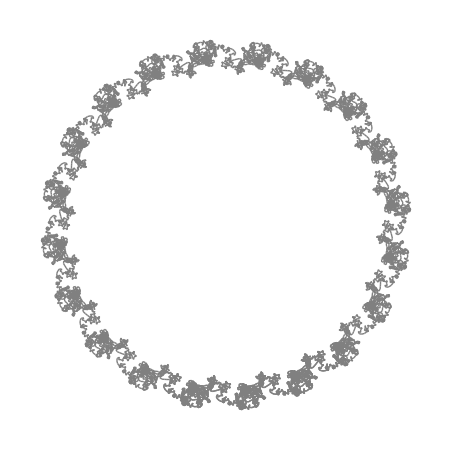

```mathematica
f[n_]:=1/59 n^3+1/9 n^2+1/20 n
f[n_]:=1/59 n^3+1/(2 9)n^2+1/20 n
g[n_]:=ⅇ^(2 π ⅈ f[n])
10260;
ls1=Accumulate[Table[ReIm[g[i]]//N,{i,1,12520}]];
ls2={};
For[i=1,i<Length[ls1],i++,AppendTo[ls2,Line[{ls1[[i]],ls1[[i+1]]}]]]
Graphics[{Gray,ls2}]
```

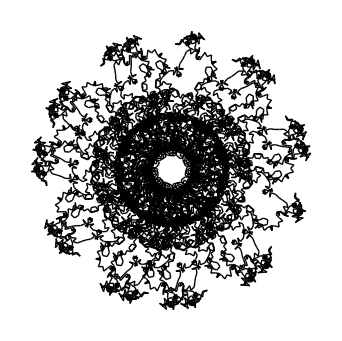
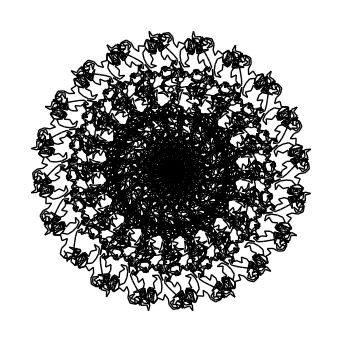
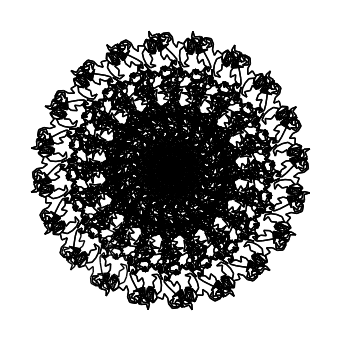

```mathematica
31/504.
Sum[(2n-1)^5/(1+ⅇ^(π (2n-1))),{n,1,7}]//N
```

0.0615079

0.0615079

```mathematica
Mod[3 21493760,24]
```

0

```mathematica
f[n_]:=1/59 n^3+1/(1 9)n^2+1/20 n
g[n_]:=1/59 n^3+1/(2 9)n^2+1/20 n
Table[{x,Mod[f[x],2π]//N,Mod[g[x],2π]//N},{x,1,20}]//tf
```

1 | 0.17806 | 0.122505
2 | 0.680038 | 0.457815
3 | 1.60763 | 1.10763
4 | 3.06252 | 2.17363
5 | 5.14642 | 3.75753
6 | 1.67783 | 5.96102
7 | 5.32482 | 2.6026
8 | 3.62271 | 0.067151
9 | 2.95638 | 4.73956
10 | 3.42752 | 4.15515
11 | 5.13784 | 4.6988
12 | 1.90584 | 0.189024
13 | 0.116398 | 3.29388
14 | 6.1544 | 1.5487
15 | 1.27198 | 1.33835
16 | 4.42039 | 2.76454
17 | 3.13496 | 5.92896
18 | 3.80057 | 4.65012
19 | 0.235716 | 5.3129
20 | 5.10848 | 1.73581

tmp